Harlan Brawer, 704924872, harlanbrawer@gmail.com,hw4

```mathematica
Remove["Global`*"]//Quiet
r:={{c t},
{x},
{y},
{z}}; (* lab frame *)
r':={{c t'},
{x'},
{y'},
{z'}}; (* rocket frame *)
A:={{γ,γ β,0,0},
{γ β,γ,0,0},
{0,0,1,0},
{0,0,0,1}}; (* transformation matrix *)
β=-v/c;
γ=1/Sqrt[1-β^2];
(*r=A.r'*)

(* 1 *)
Inverse[A]
```

{{1/(√(1-v^2/c^2) (1/(1-v^2/c^2)-v^2/(c^2 (1-v^2/c^2)))),v/(c √(1-v^2/c^2) (1/(1-v^2/c^2)-v^2/(c^2 (1-v^2/c^2)))),0,0},{v/(c √(1-v^2/c^2) (1/(1-v^2/c^2)-v^2/(c^2 (1-v^2/c^2)))),1/(√(1-v^2/c^2) (1/(1-v^2/c^2)-v^2/(c^2 (1-v^2/c^2)))),0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
(* 2 *)
Remove["Global`*"]//Quiet
r:={{c t},
{x},
{y},
{z}}; (* lab frame *)
r':={{c t'},
{x'},
{y'},
{z'}}; (* rocket frame *)
A:={{γ,γ β,0,0},
{γ β,γ,0,0},
{0,0,1,0},
{0,0,0,1}}; (* transformation matrix *)
β=-v/c;
γ=1/Sqrt[1-β^2];
(*r=A.r'*)

(* i *)
r'={{c t'},
{c t' Sin[θ'] Cos[φ']},
{c t' Sin[θ'] Sin[φ']},
{c t' Cos[θ']}};

(* ii *)
r'[[2]]^2+r'[[3]]^2+r'[[4]]^2//Simplify
r=A.r';
r[[2]]^2+r[[3]]^2+r[[4]]^2//Simplify
```

{c^2 (t')^2}

{(c^2 (c-v Cos[φ'] Sin[θ'])^2 (t')^2)/(c^2-v^2)}

```mathematica
(* 3 *)
Remove["Global`*"]//Quiet
(* lorentz transforms *)
x'=γ*(x-v*t);
y'=y;
z'=z;
t'=γ*(t-v*x/c^2);

(* i *)
t1'=γ*(t1-v*x1/c^2);
t2'=γ*(t2-v*x1/c^2);
t2'-t1'//Simplify

(* ii *)
t1a'=γ*(t1-v*x1/c^2);
t1b'=γ*(t1-v*x2/c^2);
t1-t1
Print["same time in rocket frame"]
t1b'-t1a'//Simplify
Print["not zero so do not occur at same time in lab frame"]


(* iii *)
x1'=γ*(x1-v*t1);
x2'=γ*(x2-v*t1);
x2'-x1'//Simplify

(* iv *)

Animate[
ListLinePlot[{{0,0},{1/γ,.3}}],
{γ,1,10}
]
```

(-t1+t2) γ

0

same time in rocket frame

(v (x1-x2) γ)/c^2

not zero so do not occur at same time in lab frame

(-x1+x2) γ

```mathematica
(* 4 *)
Remove["Global`*"]//Quiet

Lx=γ*L0*Cos[θ0];
Ly=L0*Sin[θ0];
L=Sqrt[Lx^2+Lx^2];
θ=ArcTan[Ly/Lx];

(* i *)
time = L/u

(* ii *)
L

(* iii *)
Vcr=u*Cos[θ];
Vro=v;
Vco = (Vcr+Vro)/(1+Vcr*Vro/c^2)

(* 4 *)
L/L0//Simplify
```

(√2 √(L0^2 γ^2 Cos[θ0]^2))/u

√2 √(L0^2 γ^2 Cos[θ0]^2)

(v+u/(√(1+Tan[θ0]^2/γ^2)))/(1+(u v)/(c^2 √(1+Tan[θ0]^2/γ^2)))

(√2 √(L0^2 γ^2 Cos[θ0]^2))/L0

```mathematica
(* 5 *)
Remove["Global`*"]//Quiet
(* i *)
r'={{c t'},
{ux'},
{uy'},
{uz'}} (* rocket frame *)

(* ii *)
A={{γ,γ β,0,0},
{γ β,γ,0,0},
{0,0,1,0},
{0,0,0,1}}; (* transformation matrix *)
r=A.r'

(* iii *)
(*{{c γ t'+β γ ux'},{c β γ t'+γ ux'},{uy'},{uz'}}*)
t'=γ*(t-β*x/c);
x'=γ*(x-v*t);
deriv =D[t',t];
Dt[{{c γ t'+β γ ux'},{c β γ t'+γ ux'},{uy'},{uz'}},t]
```

{{c t'},{ux'},{uy'},{uz'}}

{{c γ t'+β γ ux'},{c β γ t'+γ ux'},{uy'},{uz'}}

{{(t-(x β)/c) γ^2 Dt[c,t]+c γ^2 (1+(x β Dt[c,t])/c^2-(β Dt[x,t])/c-(x Dt[β,t])/c)+2 c (t-(x β)/c) γ Dt[γ,t]+γ Dt[β,t] ux'+β Dt[γ,t] ux'+β γ Dt[ux,t]'},{β (t-(x β)/c) γ^2 Dt[c,t]+c (t-(x β)/c) γ^2 Dt[β,t]+c β γ^2 (1+(x β Dt[c,t])/c^2-(β Dt[x,t])/c-(x Dt[β,t])/c)+2 c β (t-(x β)/c) γ Dt[γ,t]+Dt[γ,t] ux'+γ Dt[ux,t]'},{Dt[uy,t]'},{Dt[uz,t]'}}

```mathematica
(* 6 *)
Remove["Global`*"]//Quiet
(* i *)
A={{γ,γ β,0,0},
{γ β,γ,0,0},
{0,0,1,0},
{0,0,0,1}}; (* transformation matrix *)
r1'={{c t1'},
{x1'},
{y1'},
{z1'}}; (* lab frame *)
r2'={{c t2'},
{x2'},
{y2'},
{z2'}}; (* lab frame *)
r1=A.r1';
r2=A.r2';
γ=1/Sqrt[1-β^2];
r1'[[1]]*r2'[[1]]-r1'[[4]]*r2'[[4]]-r1'[[2]]*r2'[[2]]-r1'[[3]]*r2'[[3]]//Simplify
r1[[1]]*r2[[1]]-r1[[4]]*r2[[4]]-r1[[2]]*r2[[2]]-r1[[3]]*r2[[3]]//Simplify

(* iii *)
Print["gamma must be infinity so they must move at c"]
```

{{-1/(-1+β^2)((-1+β^2) {{(c t1'+β x1')/(√(1-β^2))},{(c β t1'+x1')/(√(1-β^2))},{y1'},{z1'}}'⟦2⟧ {{(c t2'+β x2')/(√(1-β^2))},{(c β t2'+x2')/(√(1-β^2))},{y2'},{z2'}}'⟦2⟧+(-1+β^2) {{(c t1'+β x1')/(√(1-β^2))},{(c β t1'+x1')/(√(1-β^2))},{y1'},{z1'}}'⟦3⟧ {{(c t2'+β x2')/(√(1-β^2))},{(c β t2'+x2')/(√(1-β^2))},{y2'},{z2'}}'⟦3⟧-{{(c t1'+β x1')/(√(1-β^2))},{(c β t1'+x1')/(√(1-β^2))},{y1'},{z1'}}'⟦4⟧ {{(c t2'+β x2')/(√(1-β^2))},{(c β t2'+x2')/(√(1-β^2))},{y2'},{z2'}}'⟦4⟧+β^2 {{(c t1'+β x1')/(√(1-β^2))},{(c β t1'+x1')/(√(1-β^2))},{y1'},{z1'}}'⟦4⟧ {{(c t2'+β x2')/(√(1-β^2))},{(c β t2'+x2')/(√(1-β^2))},{y2'},{z2'}}'⟦4⟧+c^2 t1' t2'+c β t2' x1'+c β t1' x2'+β^2 x1' x2')},{-1/(-1+β^2)((-1+β^2) {{(c t1'+β x1')/(√(1-β^2))},{(c β t1'+x1')/(√(1-β^2))},{y1'},{z1'}}'⟦2⟧ {{(c t2'+β x2')/(√(1-β^2))},{(c β t2'+x2')/(√(1-β^2))},{y2'},{z2'}}'⟦2⟧+(-1+β^2) {{(c t1'+β x1')/(√(1-β^2))},{(c β t1'+x1')/(√(1-β^2))},{y1'},{z1'}}'⟦3⟧ {{(c t2'+β x2')/(√(1-β^2))},{(c β t2'+x2')/(√(1-β^2))},{y2'},{z2'}}'⟦3⟧-{{(c t1'+β x1')/(√(1-β^2))},{(c β t1'+x1')/(√(1-β^2))},{y1'},{z1'}}'⟦4⟧ {{(c t2'+β x2')/(√(1-β^2))},{(c β t2'+x2')/(√(1-β^2))},{y2'},{z2'}}'⟦4⟧+β^2 {{(c t1'+β x1')/(√(1-β^2))},{(c β t1'+x1')/(√(1-β^2))},{y1'},{z1'}}'⟦4⟧ {{(c t2'+β x2')/(√(1-β^2))},{(c β t2'+x2')/(√(1-β^2))},{y2'},{z2'}}'⟦4⟧+c^2 β^2 t1' t2'+c β t2' x1'+c β t1' x2'+x1' x2')},{-{{(c t1'+β x1')/(√(1-β^2))},{(c β t1'+x1')/(√(1-β^2))},{y1'},{z1'}}'⟦2⟧ {{(c t2'+β x2')/(√(1-β^2))},{(c β t2'+x2')/(√(1-β^2))},{y2'},{z2'}}'⟦2⟧-{{(c t1'+β x1')/(√(1-β^2))},{(c β t1'+x1')/(√(1-β^2))},{y1'},{z1'}}'⟦3⟧ {{(c t2'+β x2')/(√(1-β^2))},{(c β t2'+x2')/(√(1-β^2))},{y2'},{z2'}}'⟦3⟧-{{(c t1'+β x1')/(√(1-β^2))},{(c β t1'+x1')/(√(1-β^2))},{y1'},{z1'}}'⟦4⟧ {{(c t2'+β x2')/(√(1-β^2))},{(c β t2'+x2')/(√(1-β^2))},{y2'},{z2'}}'⟦4⟧+y1' y2'},{-{{(c t1'+β x1')/(√(1-β^2))},{(c β t1'+x1')/(√(1-β^2))},{y1'},{z1'}}'⟦2⟧ {{(c t2'+β x2')/(√(1-β^2))},{(c β t2'+x2')/(√(1-β^2))},{y2'},{z2'}}'⟦2⟧-{{(c t1'+β x1')/(√(1-β^2))},{(c β t1'+x1')/(√(1-β^2))},{y1'},{z1'}}'⟦3⟧ {{(c t2'+β x2')/(√(1-β^2))},{(c β t2'+x2')/(√(1-β^2))},{y2'},{z2'}}'⟦3⟧-{{(c t1'+β x1')/(√(1-β^2))},{(c β t1'+x1')/(√(1-β^2))},{y1'},{z1'}}'⟦4⟧ {{(c t2'+β x2')/(√(1-β^2))},{(c β t2'+x2')/(√(1-β^2))},{y2'},{z2'}}'⟦4⟧+z1' z2'}}

{c^2 t1' t2'-x1' x2'-y1' y2'-z1' z2'}

gamma must be infinity so they must move at c

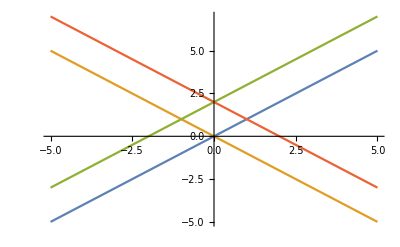

```mathematica
(* 7 *)
f1[x_]=x;
g1[x_]=-x;
f2[x_]=x+2;
g2[x_]=-x+2;
Plot[{f1[x],g1[x],f2[x],g2[x]},{x,-5,5}]
```